```mathematica
FullSimplify[ChebyshevT[27, Sin[θ]]]
```

-Sin[27 θ]

```mathematica
FullSimplify[Sin[7θ]]
```

Sin[7 θ]

```mathematica
FullSimplify[LegendreP[3, 2, Cos[θ]]]
```

15 Cos[θ] Sin[θ]^2

```mathematica
<<FourierSeries`
```

```mathematica
TrigReduce[LegendreP[4, 4, Cos[θ]]]
```

-105/8 (-3+4 Cos[2 θ]-Cos[4 θ])

```mathematica
Refine[LegendreP[5, 3, Cos[θ]],θ>0]
```

105/2 √(1-Cos[θ]^2) (-1+Cos[θ]^2) (-1+9 Cos[θ]^2)

```mathematica
FullSimplify[LegendreP[20, 13, Cos[θ]]]
```

-(2110886623587616875 (8091 Cos[θ]+5481 Cos[3 θ]+2331 Cos[5 θ]+481 Cos[7 θ]) Sin[θ]^12 √(Sin[θ]^2))/1024

```mathematica
N[Expand[TrigReduce[[LegendreP[20, 19, (1-Sin[θ]^2)^(1/2)]]]]]
```

-5.93192×10^22 √(Cos[θ]^2) √(Sin[θ]^2)+1.06775×10^23 √(Cos[θ]^2) Cos[2. θ] √(Sin[θ]^2)-7.76543×10^22 √(Cos[θ]^2) Cos[4. θ] √(Sin[θ]^2)+4.52983×10^22 √(Cos[θ]^2) Cos[6. θ] √(Sin[θ]^2)-2.09069×10^22 √(Cos[θ]^2) Cos[8. θ] √(Sin[θ]^2)+7.46676×10^21 √(Cos[θ]^2) Cos[10. θ] √(Sin[θ]^2)-1.99114×10^21 √(Cos[θ]^2) Cos[12. θ] √(Sin[θ]^2)+3.73338×10^20 √(Cos[θ]^2) Cos[14. θ] √(Sin[θ]^2)-4.39221×10^19 √(Cos[θ]^2) Cos[16. θ] √(Sin[θ]^2)+2.44012×10^18 √(Cos[θ]^2) Cos[18. θ] √(Sin[θ]^2)

```mathematica
N[Expand[TrigReduce[LegendreP[20, 20, Cos[θ]]]]]
```

5.63533×10^22-1.02461×10^23 Cos[2. θ]+7.68454×10^22 Cos[4. θ]-4.72895×10^22 Cos[6. θ]+2.36447×10^22 Cos[8. θ]-9.45789×10^21 Cos[10. θ]+2.95559×10^21 Cos[12. θ]-6.95433×10^20 Cos[14. θ]+1.15906×10^20 Cos[16. θ]-1.22006×10^19 Cos[18. θ]+6.10029×10^17 Cos[20. θ]

```mathematica
FourierTrigSeries[LegendreP[3, 2, Cos[θ]],t,3]
```

-15 Cos[θ] (-1+Cos[θ]^2)

```mathematica
x1=200;
x2=14.327;
2(-2/3(x2/2)^(3/2)-2(x2/2)^(1/2)+Log[((x2/2)^(1/2)+1)/((x2/2)^(1/2)-1)])-2(-2/3(x1/2)^(3/2)-2(x1/2)^(1/2)+Log[((x1/2)^(1/2)+1)/((x1/2)^(1/2)-1)])
```

1338.23

```mathematica
LegendreP[1,1, Cos[θ]]*Sin[θ]
```

-√(1-Cos[θ]^2) Sin[θ]

```mathematica
N[Table[(2-KroneckerDelta[j,0])/π Integrate[LegendreP[3,0, Cos[θ]]*Cos[j θ], {θ, 0, π}], {j, 0, 10}]]
```

{0.,0.375,0.,0.625,0.,0.,0.,0.,0.,0.,0.}

```mathematica
N[Table[2/π Integrate[LegendreP[3,1, Cos[θ]]*Sin[j θ], {θ, 0, π}], {j, 0, 10}]]
```

{0.,-0.375,0.,-1.875,0.,0.,0.,0.,0.,0.,0.}

```mathematica
2/π Integrate[LegendreP[3, 2, Cos[θ]]Cos[1 θ], {θ, 0, π}]
```

15/4

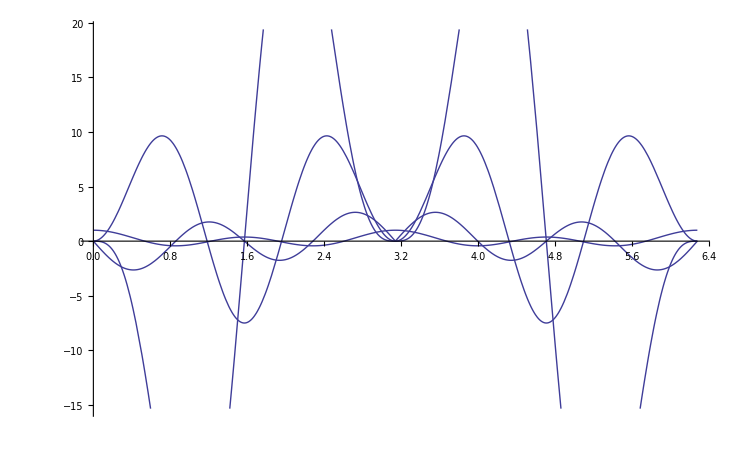

```mathematica
Plot[Table[LegendreP[4, m, Cos[θ]], {m, 0, 3}], {θ, 0, 2π}]
```

```mathematica
LegendreP[8, 8, Cos[θ]]
```

2027025 (-1+Cos[θ]^2)^4

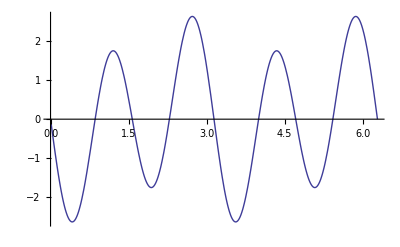

```mathematica
Plot[-5/2 Sin[θ] (-3 Cos[θ]+7 Cos[θ]^3), {θ, 0, 2π}]
```

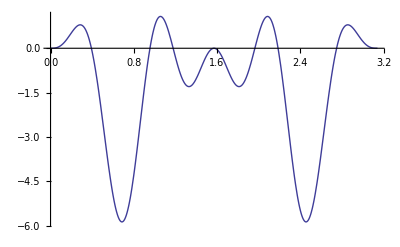

```mathematica
Plot[Cos[θ]LegendreP[5, 2, Cos[θ]]Cos[4θ]Sin[θ], {θ, 0, π}]
```

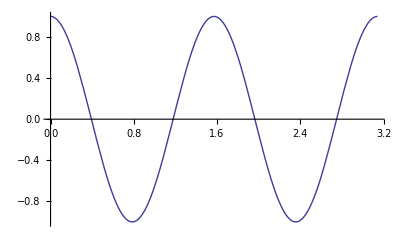

```mathematica
Plot[Cos[4θ], {θ, 0, π}]
```

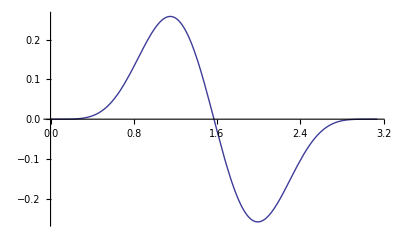

```mathematica
Plot[Sin[θ]^(4+1)Cos[θ]Cos[0θ],  {θ, 0, π}]
```

```mathematica
Integrate[Sin[θ]Cos[j θ], θ]
```

(Cos[θ] Cos[j θ]+j Sin[θ] Sin[j θ])/(-1+j^2)

```mathematica
Integrate[Cos[θ]LegendreP[6,4,  Cos[θ]]Cos[2θ]Sin[θ], {θ, 0, π}]
```

0

```mathematica
Integrate[LegendreP[6,4,  Cos[θ]]Cos[2θ]Sin[θ], {θ, 0, π}]
```

96

```mathematica
Integrate[Sin[θ]^(2j+1)Cos[n θ], {θ, 0, π},Assumptions->{n∈Integers, j∈Integers}]
```

If[j>-1,0,Integrate[Cos[n θ] Sin[θ]^(1+2 j),{θ,0,π},Assumptions→j∈Integers&&n∈Integers&&j≤-1]]

```mathematica
Integrate[Cos[3θ], {θ, 0, π}]
```

0

```mathematica
2(-2/3(6.757/2)^(3/2)-2(6.757/2)^(1/2)+Log[((6.757/2)^(1/2)+1)/((6.757/2)^(1/2)-1)])-2(-2/3(200/2)^(3/2)-2(200/2)^(1/2)+Log[((200/2)^(1/2)+1)/((200/2)^(1/2)-1)])
```

1359.74

```mathematica
2000-6.757+2Log[(2000-2)/(6.757-2)]+1359.74
```

3365.06

```mathematica
TrigReduce[LegendreP[0, m, Cos[θ]]+LegendreP[1, m, Cos[θ]]+LegendreP[2, m, Cos[θ]]+LegendreP[3, m, Cos[θ]]+LegendreP[4, m, Cos[θ]]+LegendreP[5, m, Cos[θ]]]
```

105/16 (6+18 Cos[θ]-8 Cos[2 θ]-27 Cos[3 θ]+2 Cos[4 θ]+9 Cos[5 θ])

```mathematica
N[Re[Table[((-1)^(j/2)m!(2*m-1)!!π)/(2^m((m+j)/2)!((m-j)/2)!), {j, 0, 8}, {m, 0, 8, 2}]]]//MatrixForm
```

(3.14159 | 4.71239 | 123.7 | 10205.3 | 1.74127×10^6
0. | 0. | 0. | 0. | 0.
0. | -2.35619 | -82.4668 | -7653.95 | -1.39302×10^6
0. | 0. | 0. | 0. | 0.
0. | 0. | 20.6167 | 3061.58 | 696509.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -510.263 | -199003.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 24875.3)

```mathematica
N[Re[Table[(2-KroneckerDelta[0, j])/π((-1)^(j/2)m!(2*m-1)!!π)/(2^m((m+j)/2)!((m-j)/2)!), {j, 0, 8}, {m, 0, 8, 2}]]]//MatrixForm
```

(1. | 1.5 | 39.375 | 3248.44 | 554265.
0. | 0. | 0. | 0. | 0.
0. | -1.5 | -52.5 | -4872.66 | -886823.
0. | 0. | 0. | 0. | 0.
0. | 0. | 13.125 | 1949.06 | 443412.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -324.844 | -126689.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 15836.1)

```mathematica
N[Table[(2-KroneckerDelta[0, j])/π Integrate[LegendreP[m,m,  Cos[θ]]Cos[j*θ], {θ, 0, π}], {j, 0, 8}, {m, 0, 8, 2}]]//MatrixForm
```

(1. | 1.5 | 39.375 | 3248.44 | 554265.
0. | 0. | 0. | 0. | 0.
0. | -1.5 | -52.5 | -4872.66 | -886823.
0. | 0. | 0. | 0. | 0.
0. | 0. | 13.125 | 1949.06 | 443412.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -324.844 | -126689.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 15836.1)

```mathematica
n=0;
m=0;
NIntegrate[Sin[θ]^(2*n+1)Sin[(2*m+1)*θ], {θ, 0, π}]
```

1.5708

```mathematica
N[Table[Integrate[LegendreP[m,m,  Cos[θ]]Sin[j*θ], {θ, 0, π}], {j, 0, 8}, {m, 1, 8, 2}], 18]//MatrixForm
```

(0 | 0 | 0 | 0
-1.5707963267948966 | -17.671458676442587 | -927.75158051323582 | -116084.91651171863
0 | 0 | 0 | 0
0 | 5.89048622548086232 | 463.87579025661791 | 69650.9499070311789
0 | 0 | 0 | 0
0 | 0 | -92.7751580513235816 | -23216.9833023437263
0 | 0 | 0 | 0
0 | 0 | 0 | 3316.711900334818
0 | 0 | 0 | 0)

```mathematica
m=3;
N[Table[ Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0.
-17.6715 | 0. | -30.9251 | 0. | -43.4884 | 0.
0. | -41.2334 | 0. | -69.5814 | 0. | -95.6744
5.89049 | 0. | -67.0043 | 0. | -113.07 | 0.
0. | 20.6167 | 0. | -92.7752 | 0. | -159.457
0. | 0. | 46.3876 | 0. | -116.935 | 0.
0. | 0. | 0. | 85.0439 | 0. | -138.196
0. | 0. | 0. | 0. | 138.196 | 0.
0. | 0. | 0. | 0. | 0. | 207.294)

```mathematica
m=6;
N[Table[ Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ], {θ, 0, π}], {j, 0, 8}, {l, 0, 8}], 25]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 10205.26738564559397306849 | 0 | 58042.45825585931572182705
0 | 0 | 0 | 0 | 0 | 0 | 0 | 16583.5595016740902062363 | 0
0 | 0 | 0 | 0 | 0 | 0 | -7653.95053923419547980137 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -29850.40710301336237122534 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3061.580215693678191920548 | 0 | -69650.94990703117886619247
0 | 0 | 0 | 0 | 0 | 0 | 0 | 16583.5595016740902062363 | 0
0 | 0 | 0 | 0 | 0 | 0 | -510.2633692822796986534247 | 0 | 53067.39040535708865995616
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3316.71190033481804124726 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -12437.66962625556765467723)

```mathematica
m=4;
(A=N[Table[(2-KroneckerDelta[0, j])/π Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ], {θ, 0, π}], {j, 0, 8}, {l, 0, 8}]])//MatrixForm
```

(0. | 0. | 0. | 0. | 39.375 | 0. | 147.656 | 0. | 355.298
0. | 0. | 0. | 0. | 0. | 118.125 | 0. | 406.055 | 0.
0. | 0. | 0. | 0. | -52.5 | 0. | 73.8281 | 0. | 406.055
0. | 0. | 0. | 0. | 0. | -177.188 | 0. | -81.2109 | 0.
0. | 0. | 0. | 0. | 13.125 | 0. | -383.906 | 0. | -365.449
0. | 0. | 0. | 0. | 0. | 59.0625 | 0. | -676.758 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 162.422 | 0. | -1055.74
0. | 0. | 0. | 0. | 0. | 0. | 0. | 351.914 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 659.839)

```mathematica
m=4;
(B=N[Table[(2*l+1)/2((l-m)!)/((l+m)!)Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{l, m, 8}, {j, 0, 8}]])//MatrixForm
```

(0.0125 | 0. | -0.00892857 | 0. | 0.00297619 | 0. | -0.000270563 | 0. | -0.0000208125
0. | 0.00218254 | 0. | -0.00363757 | 0. | 0.00165344 | 0. | -0.000178063 | 0.
0.00103175 | 0. | 0.000343915 | 0. | -0.00171958 | 0. | 0.000998076 | 0. | -0.000122655
0. | 0.000396825 | 0. | -0.000036075 | 0. | -0.000901876 | 0. | 0.000641026 | 0.
0.000224868 | 0. | 0.000143098 | 0. | -0.000102213 | 0. | -0.000511063 | 0. | 0.000432068)

```mathematica
A.B//MatrixForm
```

(0.724426 | 0. | -0.249939 | 0. | -0.173035 | 0. | -0.0448608 | 0. | 0.134583
0. | 0.418945 | 0. | -0.444336 | 0. | -0.170898 | 0. | 0.239258 | 0.
-0.48877 | 0. | 0.552246 | 0. | -0.324707 | 0. | -0.119629 | 0. | 0.16748
0. | -0.418945 | 0. | 0.647461 | 0. | -0.219727 | 0. | -0.0205078 | 0.
-0.314209 | 0. | -0.301514 | 0. | 0.736572 | 0. | -0.199951 | 0. | -0.111084
0. | -0.139648 | 0. | -0.19043 | 0. | 0.708008 | 0. | -0.444336 | 0.
-0.0698242 | 0. | -0.0952148 | 0. | -0.171387 | 0. | 0.70166 | 0. | -0.476074
0. | 0.139648 | 0. | -0.0126953 | 0. | -0.317383 | 0. | 0.225586 | 0.
0.148376 | 0. | 0.0944214 | 0. | -0.0674438 | 0. | -0.337219 | 0. | 0.285095)

```mathematica
B.A//MatrixForm
```

(1. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 6.93889×10^-17 | 0.
0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 1. | 0.
-8.67362×10^-19 | 0. | 0. | 0. | 1.)

```mathematica
m=5;
(A=N[Table[2/π Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ], {θ, 0, π}], {j, 0, 8}, {l, 0, 8}]])//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -590.625 | 0. | -2030.27 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1624.22 | 0. | -5278.71
0. | 0. | 0. | 0. | 0. | 295.313 | 0. | -2679.96 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1299.38 | 0. | -3167.23
0. | 0. | 0. | 0. | 0. | -59.0625 | 0. | 3492.07 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -324.844 | 0. | 7390.2
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1055.74 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2639.36)

```mathematica
m=4;
(A=N[Table[(2-KroneckerDelta[0, j])/π Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]])//MatrixForm
(B=N[Table[(2*l+1)/2((l-m)!)/((l+m)!)Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{l, m, 8}, {j, 0, 8}]])//MatrixForm
```

```mathematica
N[%, 18]
```

{{1.65859×10^186,0.,-1.62639×10^186,0.,1.53345×10^186,0.,-1.39014×10^186,0.,1.21159×10^186,0.,-1.01511×10^186,0.,8.17481×10^185,0.,-6.32659×10^185,0.,4.70439×10^185,0.,-3.36028×10^185,0.,2.30498×10^185,0.,-1.51792×10^185,0.,9.59323×10^184,0.,-5.81637×10^184,0.,3.38161×10^184,0.,-1.88441×10^184,0.,1.00596×10^184,0.,-5.14159×10^183,0.,2.5145×10^183,0.,-1.17584×10^183,0.,5.25377×10^182,0.,-2.24112×10^182,0.,9.11904×10^181,0.,-3.53595×10^181,0.,1.30522×10^181,0.,-4.58123×10^180,0.,1.52708×10^180,0.,-4.82753×10^179,0.,1.44518×10^179,0.,-4.09015×10^178,0.,1.0924×10^178,0.,-2.74775×10^177,0.,6.49469×10^176,0.,-1.43894×10^176,0.,2.98006×10^175,0.,-5.75099×10^174,0.,1.03052×10^174,0.,-1.70773×10^173,0.,2.60501×10^172,0.,-3.63828×10^171,0.,4.62322×10^170,0.,-5.30534×10^169,0.,5.44873×10^168,0.,-4.95339×10^167,0.,3.93126×10^166,0.,-2.67573×10^165,0.,1.52503×10^164,0.,-7.03858×10^162,0.,2.50102×10^161,0.,-6.28397×10^159,0.,9.37905×10^157}}

```mathematica
{{1.6585925008490854*^186,0.,-1.626386821220948*^186,0.,1.5334504314368936*^186,0.,-1.3901373070035392*^186,0.,1.2115875611498735*^186,0.,-1.0151139025850292*^186,0.,8.174811073914837*^185,0.,-6.326592918073221*^185,0.,4.7043896057467544*^185,0.,-3.3602782898191103*^185,0.,2.3049842814461665*^185,0.,-1.5179164780255244*^185,0.,9.593232141121313*^184,0.,-5.816369093435757*^184,0.,3.381609938044045*^184,0.,-1.8844085914291244*^184,0.,1.0059624811388559*^184,0.,-5.141586014709708*^183,0.,2.514498269967521*^183,0.,-1.1758445147330135*^183,0.,5.2537733637006985*^182,0.,-2.2411201061940044*^182,0.,9.119040432099741*^181,0.,-3.535954453263165*^181,0.,1.3052180867749938*^181,0.,-4.581229046296336*^180,0.,1.5270763487654454*^180,0.,-4.827531683193988*^179,0.,1.445184644013487*^179,0.,-4.0901452189060956*^178,0.,1.0923990336208825*^178,0.,-2.7477521704574347*^177,0.,6.494686948353937*^176,0.,-1.438942617299974*^176,0.,2.980058674881603*^175,0.,-5.750990425210111*^174,0.,1.0305242958468985*^174,0.,-1.7077259759748602*^173,0.,2.6050057260633464*^172,0.,-3.638276153719757*^171,0.,4.623223841743338*^170,0.,-5.305338834787437*^169,0.,5.448726370862773*^168,0.,-4.953387609875249*^167,0.,3.931260007837499*^166,0.,-2.675726706905104*^165,0.,1.5250255842464322*^164,0.,-7.0385796195989186*^162,0.,2.501018138943778*^161,0.,-6.283965173225573*^159,0.,9.379052497351602*^157}}
```

```mathematica
For[m=0, m<1, m+=2, 
Show[N[Table[Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{l, m, 8}, {j, 0, 8}]]//MatrixForm]]
```

Show::gtype: MatrixForm is not a type of graphics.

```mathematica
m=0;
N[Table[Integrate[√((π(2l+1)(l-m)!)/((l+m)!))LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{l, m, 8}, {j, 0, 8}]]//MatrixForm
```

(3.54491 | 0. | -1.18164 | 0. | -0.236327 | 0. | -0.101283 | 0. | -0.0562684
0. | 2.04665 | 0. | -1.22799 | 0. | -0.292379 | 0. | -0.136444 | 0.
0. | 0. | 2.11377 | 0. | -1.20787 | 0. | -0.301968 | 0. | -0.146409
0. | 0. | 0. | 2.14376 | 0. | -1.19098 | 0. | -0.303158 | 0.
0. | 0. | 0. | 0. | 2.16071 | 0. | -1.17857 | 0. | -0.302197
0. | 0. | 0. | 0. | 0. | 2.17159 | 0. | -1.16932 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 2.17917 | 0. | -1.16222
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.18475 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.18903)

```mathematica
m=0;
N[Table[Integrate[2π SphericalHarmonicY[l,m,  θ, 0]Cos[j*θ]Sin[θ], {θ, 0, π}],{l, m, 8}, {j, 0, 8}]]//MatrixForm
```

(3.54491 | 0. | -1.18164 | 0. | -0.236327 | 0. | -0.101283 | 0. | -0.0562684
0. | 2.04665 | 0. | -1.22799 | 0. | -0.292379 | 0. | -0.136444 | 0.
0. | 0. | 2.11377 | 0. | -1.20787 | 0. | -0.301968 | 0. | -0.146409
0. | 0. | 0. | 2.14376 | 0. | -1.19098 | 0. | -0.303158 | 0.
0. | 0. | 0. | 0. | 2.16071 | 0. | -1.17857 | 0. | -0.302197
0. | 0. | 0. | 0. | 0. | 2.17159 | 0. | -1.16932 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 2.17917 | 0. | -1.16222
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.18475 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.18903)

```mathematica
m=0;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}], {l, m, 8}, {j, 0, 8}]]//MatrixForm
m=1;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ]Sin[θ], {θ, 0, π}], {l, m, 8}, {j, 0, 8}]]//MatrixForm
m=2;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}], {l, m, 8}, {j, 0, 8}]]//MatrixForm
m=3;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ]Sin[θ], {θ, 0, π}], {l, m, 8}, {j, 0, 8}]]//MatrixForm
m=4;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}], {l, m, 8}, {j, 0, 8}]]//MatrixForm
m=5;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ]Sin[θ], {θ, 0, π}], {l, m, 8}, {j, 0, 8}]]//MatrixForm
m=6;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}], {l, m, 8}, {j, 0, 8}]]//MatrixForm
m=7;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ]Sin[θ], {θ, 0, π}], {l, m, 8}, {j, 0, 8}]]//MatrixForm
m=8;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}], {l, m, 8}, {j, 0, 8}]]//MatrixForm
```

(3.54491 | 0. | -1.18164 | 0. | -0.236327 | 0. | -0.101283 | 0. | -0.0562684
0. | 2.04665 | 0. | -1.22799 | 0. | -0.292379 | 0. | -0.136444 | 0.
0. | 0. | 2.11377 | 0. | -1.20787 | 0. | -0.301968 | 0. | -0.146409
0. | 0. | 0. | 2.14376 | 0. | -1.19098 | 0. | -0.303158 | 0.
0. | 0. | 0. | 0. | 2.16071 | 0. | -1.17857 | 0. | -0.302197
0. | 0. | 0. | 0. | 0. | 2.17159 | 0. | -1.16932 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 2.17917 | 0. | -1.16222
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.18475 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.18903)

(0. | -2.89441 | 0. | 0.578881 | 0. | 0.0826973 | 0. | 0.0275658 | 0.
0. | 0. | -2.58883 | 0. | 0.739667 | 0. | 0.123278 | 0. | 0.0448283
0. | 0. | 0. | -2.4754 | 0. | 0.825133 | 0. | 0.150024 | 0.
0. | 0. | 0. | 0. | -2.41574 | 0. | 0.878452 | 0. | 0.168933
0. | 0. | 0. | 0. | 0. | -2.37886 | 0. | 0.914946 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -2.35377 | 0. | 0.941509
0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.3356 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.32182)

(3.23604 | 0. | -1.94163 | 0. | 0.277375 | 0. | 0.0308195 | 0. | 0.00840531
0. | 1.71235 | 0. | -2.2016 | 0. | 0.407703 | 0. | 0.0518895 | 0.
1.121 | 0. | 1.121 | 0. | -2.29538 | 0. | 0.499839 | 0. | 0.0698058
0. | 0.811319 | 0. | 0.811319 | 0. | -2.33562 | 0. | 0.569247 | 0.
0.623666 | 0. | 0.623666 | 0. | 0.623666 | 0. | -2.35365 | 0. | 0.623666
0. | 0.499332 | 0. | 0.499332 | 0. | 0.499332 | 0. | -2.36118 | 0.
0.41176 | 0. | 0.41176 | 0. | 0.41176 | 0. | 0.41176 | 0. | -2.36334)

(0. | -2.79626 | 0. | 1.1984 | 0. | -0.133155 | 0. | -0.012105 | 0.
0. | 0. | -2.3968 | 0. | 1.59786 | 0. | -0.21789 | 0. | -0.0223477
0. | -0.662439 | 0. | -1.98732 | 0. | 1.82673 | 0. | -0.288756 | 0.
0. | 0. | -0.831554 | 0. | -1.66311 | 0. | 1.97131 | 0. | -0.348904
0. | -0.282465 | 0. | -0.847395 | 0. | -1.41233 | 0. | 2.06812 | 0.
0. | 0. | -0.405473 | 0. | -0.810946 | 0. | -1.21642 | 0. | 2.13561)

(2.96588 | 0. | -2.11849 | 0. | 0.706163 | 0. | -0.0641966 | 0. | -0.0049382
0. | 1.40525 | 0. | -2.34208 | 0. | 1.06458 | 0. | -0.114647 | 0.
1.36638 | 0. | 0.455461 | 0. | -2.27731 | 0. | 1.32179 | 0. | -0.162437
0. | 0.93683 | 0. | -0.0851664 | 0. | -2.12916 | 0. | 1.51334 | 0.
0.863715 | 0. | 0.549637 | 0. | -0.392598 | 0. | -1.96299 | 0. | 1.65957)

(0. | -2.66627 | 0. | 1.48126 | 0. | -0.40398 | 0. | 0.0310754 | 0.
0. | 0. | -2.1363 | 0. | 1.94209 | 0. | -0.672263 | 0. | 0.0597567
0. | -0.93683 | 0. | -1.44783 | 0. | 2.12916 | 0. | -0.897523 | 0.
0. | 0. | -1.13242 | 0. | -0.871096 | 0. | 2.17774 | 0. | -1.08631)

(2.77514 | 0. | -2.15844 | 0. | 0.981109 | 0. | -0.22641 | 0. | 0.015094
0. | 1.19423 | 0. | -2.27989 | 0. | 1.46147 | 0. | -0.409211 | 0.
1.44158 | 0. | 0.0436842 | 0. | -1.99939 | 0. | 1.76417 | 0. | -0.582522)

(0. | -2.55337 | 0. | 1.62487 | 0. | -0.624951 | 0. | 0.12499 | 0.
0. | 0. | -1.91415 | 0. | 2.06139 | 0. | -1.03069 | 0. | 0.242516)

(2.63195 | 0. | -2.15342 | 0. | 1.15953 | 0. | -0.386511 | 0. | 0.0682077)

```mathematica
m=0;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]]//MatrixForm
m=1;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]]//MatrixForm
m=2;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]]//MatrixForm
m=3;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]]//MatrixForm
m=4;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]]//MatrixForm
m=5;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]]//MatrixForm
m=6;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]]//MatrixForm
m=7;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]]//MatrixForm
m=8;
N[Table[√((π(2l+1)(l-m)!)/((l+m)!))Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ], {θ, 0, π}], {j, 0, 8}, {l, m, 8}]]//MatrixForm
```

(5.56833 | 0. | 3.11279 | 0. | 2.34914 | 0. | 1.96063 | 0. | 1.71659
0. | 4.82231 | 0. | 2.76233 | 0. | 2.16423 | 0. | 1.8428 | 0.
0. | 0. | 4.66918 | 0. | 2.61015 | 0. | 2.05867 | 0. | 1.76563
0. | 0. | 0. | 4.60388 | 0. | 2.52493 | 0. | 1.99023 | 0.
0. | 0. | 0. | 0. | 4.56777 | 0. | 2.4704 | 0. | 1.94219
0. | 0. | 0. | 0. | 0. | 4.54487 | 0. | 2.4325 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 4.52906 | 0. | 2.40462
0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.5175 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.50866)

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-3.40989 | 0. | -0.797415 | 0. | -0.395132 | 0. | -0.246255 | 0.
0. | -3.81237 | 0. | -1.1673 | 0. | -0.635318 | 0. | -0.416163
0. | 0. | -3.98708 | 0. | -1.38296 | 0. | -0.797865 | 0.
0. | 0. | 0. | -4.08554 | 0. | -1.52476 | 0. | -0.915559
0. | 0. | 0. | 0. | -4.14888 | 0. | -1.62528 | 0.
0. | 0. | 0. | 0. | 0. | -4.1931 | 0. | -1.70032
0. | 0. | 0. | 0. | 0. | 0. | -4.22573 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -4.25081)

(3.81237 | 0. | 2.47621 | 0. | 2.00905 | 0. | 1.74094
0. | 2.52165 | 0. | 2.09084 | 0. | 1.8096 | 0.
-1.90619 | 0. | 1.65081 | 0. | 1.70769 | 0. | 1.59171
0. | -2.52165 | 0. | 1.04542 | 0. | 1.37529 | 0.
0. | 0. | -2.88891 | 0. | 0.602716 | 0. | 1.0943
0. | 0. | 0. | -3.13626 | 0. | 0.265407 | 0.
0. | 0. | 0. | 0. | -3.31494 | 0. | 0.
0. | 0. | 0. | 0. | 0. | -3.45029 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -3.55648)

(0. | 0. | 0. | 0. | 0. | 0.
-3.08838 | 0. | -1.28037 | 0. | -0.767746 | 0.
0. | -3.08838 | 0. | -1.80815 | 0. | -1.21229
1.02946 | 0. | -2.77414 | 0. | -1.99614 | 0.
0. | 1.54419 | 0. | -2.41086 | 0. | -2.02049
0. | 0. | 1.92056 | 0. | -2.06438 | 0.
0. | 0. | 0. | 2.20996 | 0. | -1.75109
0. | 0. | 0. | 0. | 2.43973 | 0.
0. | 0. | 0. | 0. | 0. | 2.62664)

(3.27572 | 0. | 2.20081 | 0. | 1.82591
0. | 1.81072 | 0. | 1.69755 | 0.
-2.18381 | 0. | 0.550202 | 0. | 1.04338
0. | -2.71608 | 0. | -0.33951 | 0.
0.545953 | 0. | -2.86105 | 0. | -0.939039
0. | 0.90536 | 0. | -2.82925 | 0.
0. | 0. | 1.21044 | 0. | -2.71278
0. | 0. | 0. | 1.47121 | 0.
0. | 0. | 0. | 0. | 1.69549)

(0. | 0. | 0. | 0.
-2.863 | 0. | -1.41463 | 0.
0. | -2.58067 | 0. | -1.88097
1.4315 | 0. | -1.86731 | 0.
0. | 2.06454 | 0. | -1.12858
-0.2863 | 0. | 2.43316 | 0.
0. | -0.516135 | 0. | 2.63336
0. | 0. | -0.735605 | 0.
0. | 0. | 0. | -0.940487)

(2.97991 | 0. | 2.03168
0. | 1.44264 | 0.
-2.23493 | 0. | 0.
0. | -2.59675 | 0.
0.893972 | 0. | -2.43802
0. | 1.44264 | 0.
-0.148995 | 0. | 1.85754
0. | -0.288528 | 0.
0. | 0. | -0.435361)

(0. | 0.
-2.69893 | 0.
0. | -2.2256
1.61936 | 0.
0. | 2.2256
-0.539787 | 0.
0. | -0.953828
0.0771124 | 0.
0. | 0.158971)

(2.782
0.
-2.2256
0.
1.1128
0.
-0.317943
0.
0.0397428)

```mathematica
m=1;
N[Table[Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ]Sin[θ], {θ, 0, π}],{l, m, 8}, {j, 0, 8}]]//MatrixForm
```

(0. | -1.33333 | 0. | 0.266667 | 0. | 0.0380952 | 0. | 0.0126984 | 0.
0. | 0. | -1.6 | 0. | 0.457143 | 0. | 0.0761905 | 0. | 0.0277056
0. | 0. | 0. | -1.82857 | 0. | 0.609524 | 0. | 0.110823 | 0.
0. | 0. | 0. | 0. | -2.03175 | 0. | 0.738817 | 0. | 0.14208
0. | 0. | 0. | 0. | 0. | -2.21645 | 0. | 0.852481 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -2.38695 | 0. | 0.954779
0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.54608 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.69585)

```mathematica
Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ]Sin[θ], {θ, 0, π}]
```

```mathematica
N[Integrate[LegendreP[101,101,  Cos[θ]]Sin[101*θ]Sin[θ], {θ, 0, π}]]
```

-9.47238×10^159

```mathematica
m=4;
N[Table[NIntegrate[Cos[θ]LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{l, m, 16}, {j, 0, 16}]]//MatrixForm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.88378}. NIntegrate obtained 1.07137×10^-14 and 1.29888×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.21502}. NIntegrate obtained -1.72085×10^-15 and 2.70774×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate :: "ncvb" will be suppressed during this calculation.

(0. | 16. | 1.07137×10^-14 | -26.6667 | 0. | 12.1212 | 1.21014×10^-14 | -1.30536 | 0. | -0.111888 | 0. | -0.0241327 | -7.99361×10^-15 | -0.00750539 | 3.55271×10^-15 | -0.00288669 | -1.11022×10^-15
144. | 0. | -48. | 0. | -65.4545 | 0. | 48.6713 | 0. | -6.37762 | -2.80886×10^-14 | -0.612094 | -4.60743×10^-15 | -0.142372 | 0. | -0.0467644 | 1.68476×10^-14 | -0.0187509
0. | 192. | 0. | -192. | 0. | -100.699 | 6.68354×10^-14 | 122.182 | 0. | -18.7182 | -7.10543×10^-14 | -1.96618 | -1.01252×10^-13 | -0.48635 | 0. | -0.167177 | 0.
352. | 0. | 160. | 0. | -416. | 0. | -115.692 | 0. | 245.43 | 0. | -42.7759 | -2.84217×10^-13 | -4.83925 | -9.27036×10^-14 | -1.26009 | 1.58096×10^-13 | -0.450161
0. | 432. | 0. | 48. | 0. | -720. | 0. | -92.7421 | 0. | 431.451 | 0. | -83.8714 | -3.2141×10^-13 | -10.0988 | -1.59872×10^-13 | -2.74699 | 2.13718×10^-13
624. | 0. | 432. | 0. | -144. | 0. | -1104. | 0. | -13.226 | 0. | 693.548 | -4.72511×10^-13 | -148.135 | 2.77112×10^-13 | -18.8136 | 0. | -5.31409
0. | 736. | 0. | 352. | 0. | -416. | 0. | -1568. | 0. | 142.365 | 0. | 1045.29 | 3.32179×10^-13 | -242.455 | -1.38023×10^-12 | -32.2504 | -1.0516×10^-12
960. | 0. | 768. | 0. | 192. | 0. | -768. | 0. | -2112. | 0. | 394.39 | 1.93268×10^-12 | 1500.53 | 1.37668×10^-12 | -374.431 | -2.5473×10^-12 | -51.8693
0. | 1104. | 0. | 720. | 0. | -48. | 0. | -1200. | 0. | -2736. | 0. | 764.019 | 5.11591×10^-13 | 2073.36 | -2.48335×10^-12 | -552.337 | -3.63087×10^-12
1360. | 0. | 1168. | 0. | 592. | 0. | -368. | 0. | -1712. | 0. | -3440. | 5.30775×10^-12 | 1273.21 | 0. | 2778.19 | -3.10862×10^-12 | -785.087
0. | 1536. | 0. | 1152. | 0. | 384. | 0. | -768. | 0. | -2304. | 0. | -4224. | 1.08642×10^-11 | 1944.67 | -4.04299×10^-12 | 3629.67 | -1.84537×10^-11
1824. | 0. | 1632. | 0. | 1056. | 0. | 96. | 0. | -1248. | 0. | -2976. | -1.13971×10^-11 | -5088. | 0. | 2801.86 | -1.51346×10^-11 | 4642.7
0. | 2032. | 0. | 1648. | 0. | 880. | 0. | -272. | 0. | -1808. | 0. | -3728. | -4.6521×10^-11 | -6032. | -2.24176×10^-11 | 3868.92 | 5.24523×10^-11)

```mathematica
m=4;
Table[(2l+1)/2((l-m)!)/((l+m)!)Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{l, m, 9}, {j, 0, 9}]//MatrixForm
```

(1/80 | 0 | -1/112 | 0 | 1/336 | 0 | -1/3696 | 0 | -1/48048 | 0
0 | 11/5040 | 0 | -11/3024 | 0 | 5/3024 | 0 | -1/5616 | 0 | -1/65520
13/12600 | 0 | 13/37800 | 0 | -13/7560 | 0 | 83/83160 | 0 | -17/138600 | 0
0 | 1/2520 | 0 | -1/27720 | 0 | -5/5544 | 0 | 1/1560 | 0 | -179/2042040
17/75600 | 0 | 17/118800 | 0 | -17/166320 | 0 | -17/33264 | 0 | 173/400400 | 0
0 | 19/166320 | 0 | 19/432432 | 0 | -19/196560 | 0 | -19/61776 | 0 | 3709/12252240)

```mathematica
m=5;
Table[(2l+1)/2((l-m)!)/((l+m)!)Integrate[LegendreP[l,m,  Cos[θ]]Sin[j*θ]Sin[θ], {θ, 0, π}],{l, m, 9}, {j, 0, 9}]//MatrixForm
```

(0 | -11/8400 | 0 | 11/15120 | 0 | -1/5040 | 0 | 1/65520 | 0 | 1/982800
0 | 0 | -13/37800 | 0 | 13/41580 | 0 | -1/9240 | 0 | 1/103950 | 0
0 | -1/15120 | 0 | -17/166320 | 0 | 5/33264 | 0 | -137/2162160 | 0 | 233/36756720
0 | 0 | -17/415800 | 0 | -17/540540 | 0 | 17/216216 | 0 | -53/1351350 | 0
0 | -19/1940400 | 0 | -323/15135120 | 0 | -19/2162160 | 0 | 19/432432 | 0 | -359/14137200)

```mathematica
FullSimplify[ArcCos[-Cos[x]]]
```

ArcCos[-Cos[x]]

```mathematica
LegendreP[0,0,  Cos[θ]]
```

1

```mathematica
m=2;
Table[Integrate[LegendreP[l,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{l, m, 9}, {j, 0, 9}]//MatrixForm
```

(4 | 0 | -12/5 | 0 | 12/35 | 0 | 4/105 | 0 | 4/385 | 0
0 | 4 | 0 | -36/7 | 0 | 20/21 | 0 | 4/33 | 0 | 36/1001
4 | 0 | 4 | 0 | -172/21 | 0 | 412/231 | 0 | 68/273 | 0
0 | 4 | 0 | 4 | 0 | -380/33 | 0 | 1204/429 | 0 | 60/143
4 | 0 | 4 | 0 | 4 | 0 | -6476/429 | 0 | 4 | 0
0 | 4 | 0 | 4 | 0 | 4 | 0 | -13524/715 | 0 | 65004/12155
4 | 0 | 4 | 0 | 4 | 0 | 4 | 0 | -55812/2431 | 0
0 | 4 | 0 | 4 | 0 | 4 | 0 | 4 | 0 | -114276/4199)

```mathematica
Integrate[LegendreP[0,0,  Cos[θ]]Cos[0*θ]Sin[θ], {θ, 0, π}]
```

2

```mathematica
m=50;
Table[Integrate[LegendreP[m,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{j, 0, 20, 2}]
Table[((-1)^(j/2)2(m+1)! (2m-1)!!)/((m-j+1)!!(m+j+1)!!), {j, 0, 20, 2}]
```

{951930160480635893432024489903786418968370408556220707740133097472000000000000,-916008267632310010661004697831945422026167751629570869712203546624000000000000,816080092981512554952531458068460466896040360542708593016326796083200000000000,-672908146844405089171385588231888455159892928868549190732760691507200000000000,513235027254207271401904262210762381054155623713300230219902222336000000000000,-361788625769359224102981693033816104677519538027408359007472058368000000000000,235449740580059177590829355783912068123465096176567344750894514176000000000000,-141269844348035506554497613470347240874079057705940406850536708505600000000000,78014690162347966306215099976161909139416793061489478409997883801600000000000,-39572668922930127836485920277763287244631706625393213686230810624000000000000,18392930626150622797239934776988570127786567868140507769656573952000000000000}

{951930160480635893432024489903786418968370408556220707740133097472000000000000,-916008267632310010661004697831945422026167751629570869712203546624000000000000,816080092981512554952531458068460466896040360542708593016326796083200000000000,-672908146844405089171385588231888455159892928868549190732760691507200000000000,513235027254207271401904262210762381054155623713300230219902222336000000000000,-361788625769359224102981693033816104677519538027408359007472058368000000000000,235449740580059177590829355783912068123465096176567344750894514176000000000000,-141269844348035506554497613470347240874079057705940406850536708505600000000000,78014690162347966306215099976161909139416793061489478409997883801600000000000,-39572668922930127836485920277763287244631706625393213686230810624000000000000,18392930626150622797239934776988570127786567868140507769656573952000000000000}

```mathematica
l=64;
m=50;
N[Table[((-1)^(j/2)2(m+1)! (2m-1)!!)/((m-j+1)!!(m+j+1)!!), {j, 0, 64, 2}]]
```

{9.5193×10^77,-9.16008×10^77,8.1608×10^77,-6.72908×10^77,5.13235×10^77,-3.61789×10^77,2.3545×10^77,-1.4127×10^77,7.80147×10^76,-3.95727×10^76,1.83929×10^76,-7.8107×10^75,3.02014×10^75,-1.05901×10^75,3.35129×10^74,-9.51602×10^73,2.40767×10^73,-5.38184×10^72,1.05162×10^72,-1.7724×10^71,2.532×10^70,-2.99484×10^69,2.83722×10^68,-2.04748×10^67,1.03408×10^66,-3.07152×10^64,2.98206×10^62,2.84006×10^60,7.96278×10^58,3.65265×10^57,2.30347×10^56,1.83462×10^55,1.75486×10^54}

```mathematica
l=6;
m=4;
N[Table[(l+m-1)/(l-m)√((π(2l+1)(l-m)!)/((l+m)!))((-1)^(j/2)2(m+1)! (2m-1)!!)/((m-j+1)!!(m+j+1)!!), {j, 0, 64, 2}]]
```

{2.39117,-1.70798,0.569326,-0.0517569,-0.0039813,-0.000796261,-0.000234194,-0.0000862821,-0.0000369781,-0.0000176852,-9.19628×10^-6,-5.10904×10^-6,-2.99496×10^-6,-1.83562×10^-6,-1.16812×10^-6,-7.67623×10^-7,-5.18664×10^-7,-3.59075×10^-7,-2.5398×10^-7,-1.83102×10^-7,-1.34275×10^-7,-9.99917×10^-8,-7.5504×10^-8,-5.77383×10^-8,-4.46655×10^-8,-3.49203×10^-8,-2.75687×10^-8,-2.19615×10^-8,-1.76412×10^-8,-1.4281×10^-8,-1.16445×10^-8,-9.5589×10^-9,-7.89648×10^-9}

```mathematica
LegendreP[0, 0, Cos[θ]]
```

1

```mathematica
(-3)!!
```

-1

```mathematica
n=7;
m=4;
Integrate[Sin[θ]^(2n+1)Cos[2*m*θ], {θ, 0, π}]
((-1)^m 2(2n+1)!)/((2n-2m+1)!!(2n+2m+1)!!)
```

4096/52003

4096/52003

```mathematica
m=42;
j=76;
Integrate[Sin[θ]^(m+1)Cos[j*θ], {θ, 0, π}]
((-1)^(j/2)2(m+1)!)/((m-j+1)!!(m+j+1)!!)
```

1099511627776/33065127017439632095839040926967124296395

1099511627776/33065127017439632095839040926967124296395

```mathematica
m=42;
j=76;
Integrate[LegendreP[m, m, Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}]
((-1)^(j/2)2(m+1)! (2m-1)!!)/((m-j+1)!!(m+j+1)!!)
```

2110982479196835571458450778962385698816000000000/118361117944981

2110982479196835571458450778962385698816000000000/118361117944981

```mathematica
Integrate[Sin[θ]^7 Cos[10*θ], {θ, 0, π}]
```

32/109395

```mathematica
Integrate[Sin[θ]^(2k+1), {θ, 0, π},Assumptions->k∈Integers&& k>0]
```

```mathematica
FullSimplify[(√π Gamma[1+k])/Gamma[3/2+k]]
```

(√π Gamma[1+k])/Gamma[3/2+k]

```mathematica
(-1)!!
```

1

```mathematica
Integrate[Sin[θ]^(2k+1)Cos[2*j*θ], {θ, 0, π}, Assumptions->{k∈Integers, j∈Integers}]
```

If[k>-1,0,Integrate[Cos[2 j θ] Sin[θ]^(1+2 k),{θ,0,π},Assumptions→j∈Integers&&k∈Integers&&k≤-1]]

```mathematica
Integrate[Sin[θ]^(2n+1)Cos[2*m*θ], {θ, 0, π}]
```

If[Re[n]>-1,(2^(-1-2 n) π Cos[m π] Gamma[2+2 n])/(Gamma[3/2-m+n] Gamma[3/2+m+n]),Integrate[Cos[2 m θ] Sin[θ]^(1+2 n),{θ,0,π},Assumptions→Re[n]≤-1]]

```mathematica
FullSimplify[(2^(-1-2 n) π Cos[m π] Gamma[2+2 n])/(Gamma[3/2-m+n] Gamma[3/2+m+n]), Assumptions->{k∈Integers, j∈Integers}]
```

(2^(-1-2 n) π Cos[m π] Gamma[2+2 n])/(Gamma[3/2-m+n] Gamma[3/2+m+n])

```mathematica
Integrate[Sin[θ]^n Cos[m*θ], {θ, 0, π}]
```

If[Re[n]>-1,(2^-n π Cos[(m π)/2] Gamma[1+n])/(Gamma[1/2 (2-m+n)] Gamma[1/2 (2+m+n)]),Integrate[Cos[m θ] Sin[θ]^n,{θ,0,π},Assumptions→Re[n]≤-1]]

```mathematica
Integrate[Sin[θ]^n Sin[m*θ], {θ, 0, π}]
```

If[Re[n]>-2,1/(2 Gamma[1/2 (2+m+n)])((2^-n ⅇ^(-1/2 ⅈ m π) (ⅈ ⅇ^(1/2 ⅈ (m+3 n) π) (m^2-n^2) π Gamma[(m-n)/2] Gamma[1/2 (-m+n)]+Gamma[1/2 (2+m+n)] (2 ⅈ ⅇ^(1/2 ⅈ (m+3 n) π) (m+n) π Gamma[-m/2-n/2]+(-1+ⅇ^(2 ⅈ n π)) Gamma[-n] Gamma[1/2 (-m+n)] ((m-n) Hypergeometric2F1[1/2 (-m-n),-n,1/2 (2-m-n),-1]+ⅇ^(ⅈ m π) (m+n) Hypergeometric2F1[(m-n)/2,-n,1/2 (2+m-n),-1]))))/((-1+ⅇ^(2 ⅈ n π)) (-m^2+n^2) Gamma[-n] Gamma[1/2 (-m+n)])+1/((m+n) Gamma[-m])(2 m Cos[(m π)/2] Gamma[-m] Gamma[1/2 (2+m+n)] HypergeometricPFQ[{1,1/2-m/2,1-m/2},{3/2,1-m/2-n/2},1]+(m+n) (2 Cos[m π+(n π)/2] Gamma[-1-m-n] Gamma[1+n] Gamma[1/2 (2+m+n)] Hypergeometric2F1[(1+n)/2,(2+n)/2,1/2 (3+m+n),1]+√π Gamma[-m] Gamma[1/2 (1+m+n)] Hypergeometric2F1[(1-m)/2,-m/2,1/2 (1-m-n),1] Sin[(m π)/2]))),Integrate[Sin[θ]^n Sin[m θ],{θ,0,π},Assumptions→Re[n]≤-2]]

```mathematica
FullSimplify[1/(2 Gamma[1/2 (2+m+n)])((2^-n ⅇ^(-1/2 ⅈ m π) (ⅈ ⅇ^(1/2 ⅈ (m+3 n) π) (m^2-n^2) π Gamma[(m-n)/2] Gamma[1/2 (-m+n)]+Gamma[1/2 (2+m+n)] (2 ⅈ ⅇ^(1/2 ⅈ (m+3 n) π) (m+n) π Gamma[-m/2-n/2]+(-1+ⅇ^(2 ⅈ n π)) Gamma[-n] Gamma[1/2 (-m+n)] ((m-n) Hypergeometric2F1[1/2 (-m-n),-n,1/2 (2-m-n),-1]+ⅇ^(ⅈ m π) (m+n) Hypergeometric2F1[(m-n)/2,-n,1/2 (2+m-n),-1]))))/((-1+ⅇ^(2 ⅈ n π)) (-m^2+n^2) Gamma[-n] Gamma[1/2 (-m+n)])+1/((m+n) Gamma[-m])(2 m Cos[(m π)/2] Gamma[-m] Gamma[1/2 (2+m+n)] HypergeometricPFQ[{1,1/2-m/2,1-m/2},{3/2,1-m/2-n/2},1]+(m+n) (2 Cos[m π+(n π)/2] Gamma[-1-m-n] Gamma[1+n] Gamma[1/2 (2+m+n)] Hypergeometric2F1[(1+n)/2,(2+n)/2,1/2 (3+m+n),1]+√π Gamma[-m] Gamma[1/2 (1+m+n)] Hypergeometric2F1[(1-m)/2,-m/2,1/2 (1-m-n),1] Sin[(m π)/2]))), Assumptions->{m∈Integers, n∈Integers}]
```

FullSimplify::infd: Expression 2^-n\ « 1 »\ (ⅈ\ ⅇ^1/2\ ⅈ\ (m + 3\ n)\ π\ (m^2 - n^2)\ π\ Gamma[m - n/2]\ Gamma[1/2\ (-m + n)] + Gamma[1/2\ (2 + m + n)]\ (2\ « 4 »\ Gamma[Times[« 2 »] + « 1 »] + « 1 »))/(-1 + ⅇ^2\ ⅈ\ n\ π)\ (-m^2 + n^2)\ Gamma[-n]\ Gamma[1/2\ (-m + n)] simplified to ComplexInfinity.

FullSimplify::infd: Expression 2^-n\ « 1 »\ (ⅈ\ ⅇ^1/2\ ⅈ\ (m + Times[« 2 »])\ π\ (m^2 - n^2)\ π\ Gamma[1/2\ (m + Times[« 2 »])]\ Gamma[1/2\ (Times[« 2 »] + n)] + Gamma[1/2\ (« 1 »)]\ (« 1 »))/(-1 + ⅇ^2\ ⅈ\ n\ π)\ (-m^2 + n^2)\ Gamma[-n]\ Gamma[1/2\ (-m + n)] + 2\ « 4 »\ HypergeometricPFQ[« 1 »] + « 1 »/(m + n)\ Gamma[-m] simplified to ComplexInfinity.

FullSimplify::infd: Expression 2^-n\ ⅇ^-1/2\ ⅈ\ m\ π\ (« 1 »)/(-1 + ⅇ^2\ ⅈ\ n\ π)\ (-m^2 + n^2)\ « 1 »\ Gamma[1/2\ (Times[« 2 »] + n)] + 2\ « 4 »\ « 17 »[« 1 »] + « 1 »/(m + n)\ Gamma[-m]/2\ Gamma[1/2\ (2 + m + n)] simplified to ComplexInfinity.

General::stop: Further output of FullSimplify :: "infd" will be suppressed during this calculation.

ComplexInfinity

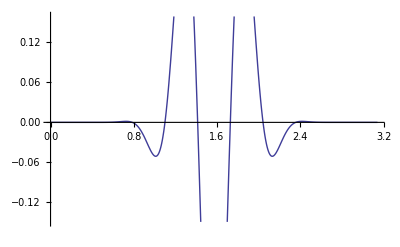

-0.00743364

-0.0467069

```mathematica
j=10;
l=12;
m=12;
Plot[SphericalHarmonicY[l, m, θ, 0]Cos[j θ]Sin[θ],  {θ, 0, π}]
N[Integrate[SphericalHarmonicY[l, m, θ, 0]Cos[j θ]Sin[θ],  {θ, 0, π}]]
N[√((π(2l+1)(l-m)!)/((l+m)!))((-1)^(j/2)2(m+1)! (2m-1)!!)/((m-j+1)!!(m+j+1)!!)]
```

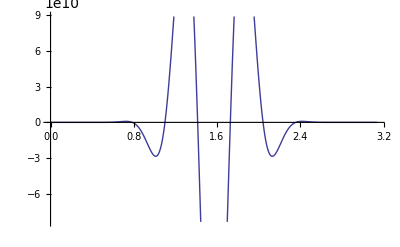

-4.15135×10^9

-4.15135×10^9

```mathematica
j=10;
l=12;
m=12;
Plot[LegendreP[l, m, Cos[θ]]Cos[j θ]Sin[θ],  {θ, 0, π}]
N[Integrate[LegendreP[l, m, Cos[θ]]Cos[j θ]Sin[θ],  {θ, 0, π}]]
N[((-1)^(j/2)2(m+1)! (2m-1)!!)/((m-j+1)!!(m+j+1)!!)]
```

```mathematica
N[√((π(2m+1))/((2m)!))((-1)^(j/2)2(m+1)! (2m-1)!!)/((m-j+1)!!(m+j+1)!!)]
```

-0.0467069

```mathematica
N[Table[Integrate[LegendreP[m,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{m, 0, 10, 2}, {j, 0, 10, 2}]]//MatrixForm
```

(2. | -0.666667 | -0.133333 | -0.0571429 | -0.031746 | -0.020202
4. | -2.4 | 0.342857 | 0.0380952 | 0.0103896 | 0.003996
112. | -80. | 26.6667 | -2.42424 | -0.18648 | -0.037296
9504. | -7392. | 3360. | -775.385 | 51.6923 | 3.04072
1.64736×10^6 | -1.34784×10^6 | 725760. | -241920. | 42691.8 | -2246.93
4.83725×10^8 | -4.09306×10^8 | 2.45583×10^8 | -1.01123×10^8 | 2.66112×10^7 | -3.8016×10^6)

```mathematica
N[Table[((-1)^(j/2)2(m+1)! (2m-1)!!)/((m-j+1)!!(m+j+1)!!),{m, 0, 10, 2}, {j, 0, 10, 2}]]//MatrixForm
```

(2. | -0.666667 | -0.133333 | -0.0571429 | -0.031746 | -0.020202
4. | -2.4 | 0.342857 | 0.0380952 | 0.0103896 | 0.003996
112. | -80. | 26.6667 | -2.42424 | -0.18648 | -0.037296
9504. | -7392. | 3360. | -775.385 | 51.6923 | 3.04072
1.64736×10^6 | -1.34784×10^6 | 725760. | -241920. | 42691.8 | -2246.93
4.83725×10^8 | -4.09306×10^8 | 2.45583×10^8 | -1.01123×10^8 | 2.66112×10^7 | -3.8016×10^6)

```mathematica
m=2;
j=0;
N[((-1)^(j/2)2(m+1)! (2m-1)!!)/((m-j+1)!!(m+j+1)!!)]
```

4.

```mathematica
N[Table[Integrate[Cos[θ]LegendreP[m+1,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{m, 0, 10, 2}, {j, 0, 10, 2}], 18]//MatrixForm
```

(0.666666666666666667 | 0.133333333333333333 | -0.247619047619047619 | -0.0698412698412698413 | -0.0352092352092352092 | -0.021534021534021534
4. | -0.571428571428571429 | -2.09523809523809524 | 0.536796536796536797 | 0.0785880785880785881 | 0.025308025308025308
144. | -48. | -65.4545454545454545 | 48.6713286713286713 | -6.37762237762237762 | -0.6120937885643768
13728. | -6240. | -4704. | 6048. | -2174.11764705882353 | 189.325077399380805
2.54592×10^6 | -1.37088×10^6 | -587520. | 1.2096×10^6 | -674829.473684210526 | 161886.315789473684
7.814016×10^8 | -4.6884096×10^8 | -1.0112256×10^8 | 3.6723456×10^8 | -2.7143424×10^8 | 1.0065975652173913×10^8)

```mathematica
Table[NIntegrate[Cos[θ]LegendreP[m+1,m,  Cos[θ]]Cos[j*θ]Sin[θ], {θ, 0, π}],{m, 0, 10, 2}, {j, 0, 10, 2}]//MatrixForm
```

(0.666667 | 0.133333 | -0.247619 | -0.0698413 | -0.0352092 | -0.021534
4. | -0.571429 | -2.09524 | 0.536797 | 0.0785881 | 0.025308
144. | -48. | -65.4545 | 48.6713 | -6.37762 | -0.612094
13728. | -6240. | -4704. | 6048. | -2174.12 | 189.325
2.54592×10^6 | -1.37088×10^6 | -587520. | 1.2096×10^6 | -674829. | 161886.
7.81402×10^8 | -4.68841×10^8 | -1.01123×10^8 | 3.67235×10^8 | -2.71434×10^8 | 1.0066×10^8)

```mathematica
N[Table[Integrate[LegendreP[m,m,  Cos[θ]]Sin[j*θ]Sin[θ], {θ, 0, π}],{m, 1, 10, 2}, {j, 0, 10, 1}]]//MatrixForm
```

(0. | -1.33333 | 0. | 0.266667 | 0. | 0.0380952 | 0. | 0.0126984 | 0. | 0.00577201 | 0.
0. | -16. | 0. | 6.85714 | 0. | -0.761905 | 0. | -0.0692641 | 0. | -0.015984 | 0.
0. | -864. | 0. | 480. | 0. | -130.909 | 0. | 10.0699 | 0. | 0.671329 | 0.
0. | -109824. | 0. | 69888. | 0. | -26880. | 0. | 5376. | 0. | -316.235 | 0.
0. | -2.54592×10^7 | 0. | 1.76256×10^7 | 0. | -8.22528×10^6 | 0. | 2.4192×10^6 | 0. | -381979. | 0.)

```mathematica
N[Table[((-1)^((j+1)/2)2^((m+3)/2)((m+1)/2)! m!!(2m-1)!!)/((m-j+1)!!(m+j+1)!!),{m, 1, 10, 2}, {j, 0, 10, 1}], 8]//MatrixForm
```

(1. ⅈ | -1.3333333 | -0.5 ⅈ | 0.26666667 | 0 | 0.038095238 | 0 | 0.012698413 | 0 | 0.0057720058 | 0
11.25 ⅈ | -16. | -7.5 ⅈ | 6.8571429 | 1.875 ⅈ | -0.76190476 | 0 | -0.069264069 | 0 | -0.01598402 | 0
590.625 ⅈ | -864. | -442.9688 ⅈ | 480. | 177.1875 ⅈ | -130.90909 | -29.53125 ⅈ | 10.06993 | 0 | 0.67132867 | 0
73901.953 ⅈ | -109824. | -59121.56 ⅈ | 69888. | 29560.78 ⅈ | -26880. | -8445.9375 ⅈ | 5376. | 1055.7422 ⅈ | -316.23529 | 0
1.69605×10^7 ⅈ | -2.54592×10^7 | -1.413375×10^7 ⅈ | 1.76256×10^7 | 8.076428×10^6 ⅈ | -8.22528×10^6 | -3.0286604×10^6 ⅈ | 2.4192×10^6 | 673035.6 ⅈ | -381978.9 | -67303.564 ⅈ)

## Testing functions

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]
SphericalHarmonicY[1,0,θ,ϕ]
SphericalHarmonicY[1,1,θ,ϕ]
SphericalHarmonicY[2,0,θ,ϕ]
SphericalHarmonicY[2,1,θ,ϕ]
SphericalHarmonicY[2,2,θ,ϕ]
```

1/(2 √π)

1/2 √(3/π) Cos[θ]

-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ]

1/4 √(5/π) (-1+3 Cos[θ]^2)

-1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ]

1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2

```mathematica
f[θ_, ϕ_]:=SphericalHarmonicY[0,0,θ,ϕ]+SphericalHarmonicY[1,0,θ,ϕ]+SphericalHarmonicY[1,1,θ,ϕ]+SphericalHarmonicY[2,0,θ,ϕ]+SphericalHarmonicY[2,1,θ,ϕ]+SphericalHarmonicY[2,2,θ,ϕ]
```

```mathematica
TrigReduce[Re[ExpToTrig[f[θ, ϕ]]]]
```

1/(8 √π)(4-2 √5+2 √6 Im[Sin[θ] Sin[ϕ]]+2 √30 Im[Cos[θ] Sin[θ] Sin[ϕ]]-√30 Im[Sin[θ]^2 Sin[2 ϕ]]+8 √π Re[1/2 √(3/π) Cos[θ]+3/4 √(5/π) Cos[θ]^2-1/2 √(3/(2 π)) Cos[ϕ] Sin[θ]-1/2 √(15/(2 π)) Cos[θ] Cos[ϕ] Sin[θ]+1/4 √(15/(2 π)) Cos[2 ϕ] Sin[θ]^2])

```mathematica
TrigReduce[Sin[θ]^4]
```

1/8 (3-4 Cos[2 θ]+Cos[4 θ])

```mathematica
TrigReduce[4 Cos[θ]^2 Sin[θ]^2]
```

1/2 (1-Cos[4 θ])

```mathematica
TrigReduce[Cos[θ] Sin[θ]^4]
```

1/16 (2 Cos[θ]-3 Cos[3 θ]+Cos[5 θ])

```mathematica
TrigReduce[-Cos[θ] Sin[θ]^4+4 Sin[θ]^2 Cos[θ]^3]
```

1/16 (6 Cos[θ]-Cos[3 θ]-5 Cos[5 θ])

```mathematica
SphericalHarmonicY[6,6,θ,ϕ]
```

1/64 ⅇ^(6 ⅈ ϕ) √(3003/π) Sin[θ]^6

```mathematica
Table[SphericalHarmonicY[l,m,θ,ϕ], {m, 0, 6}, {l, m, 6 }]//TableForm
```

1/(2 √π) | 1/2 √(3/π) Cos[θ] | 1/4 √(5/π) (-1+3 Cos[θ]^2) | 1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) | (3 (3-30 Cos[θ]^2+35 Cos[θ]^4))/(16 √π) | 1/16 √(11/π) (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5) | 1/32 √(13/π) (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)
-1/2 ⅇ^(ⅈ ϕ) √(3/(2 π)) Sin[θ] | -1/2 ⅇ^(ⅈ ϕ) √(15/(2 π)) Cos[θ] Sin[θ] | -1/8 ⅇ^(ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) Sin[θ] | -3/8 ⅇ^(ⅈ ϕ) √(5/π) Cos[θ] (-3+7 Cos[θ]^2) Sin[θ] | -1/16 ⅇ^(ⅈ ϕ) √(165/(2 π)) (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ] | -1/16 ⅇ^(ⅈ ϕ) √(273/(2 π)) Cos[θ] (5-30 Cos[θ]^2+33 Cos[θ]^4) Sin[θ] | 
1/4 ⅇ^(2 ⅈ ϕ) √(15/(2 π)) Sin[θ]^2 | 1/4 ⅇ^(2 ⅈ ϕ) √(105/(2 π)) Cos[θ] Sin[θ]^2 | 3/8 ⅇ^(2 ⅈ ϕ) √(5/(2 π)) (-1+7 Cos[θ]^2) Sin[θ]^2 | 1/8 ⅇ^(2 ⅈ ϕ) √(1155/(2 π)) Cos[θ] (-1+3 Cos[θ]^2) Sin[θ]^2 | 1/64 ⅇ^(2 ⅈ ϕ) √(1365/π) (1-18 Cos[θ]^2+33 Cos[θ]^4) Sin[θ]^2 |  | 
-1/8 ⅇ^(3 ⅈ ϕ) √(35/π) Sin[θ]^3 | -3/8 ⅇ^(3 ⅈ ϕ) √(35/π) Cos[θ] Sin[θ]^3 | -1/32 ⅇ^(3 ⅈ ϕ) √(385/π) (-1+9 Cos[θ]^2) Sin[θ]^3 | -1/32 ⅇ^(3 ⅈ ϕ) √(1365/π) Cos[θ] (-3+11 Cos[θ]^2) Sin[θ]^3 |  |  | 
3/16 ⅇ^(4 ⅈ ϕ) √(35/(2 π)) Sin[θ]^4 | 3/16 ⅇ^(4 ⅈ ϕ) √(385/(2 π)) Cos[θ] Sin[θ]^4 | 3/32 ⅇ^(4 ⅈ ϕ) √(91/(2 π)) (-1+11 Cos[θ]^2) Sin[θ]^4 |  |  |  | 
-3/32 ⅇ^(5 ⅈ ϕ) √(77/π) Sin[θ]^5 | -3/32 ⅇ^(5 ⅈ ϕ) √(1001/π) Cos[θ] Sin[θ]^5 |  |  |  |  | 
1/64 ⅇ^(6 ⅈ ϕ) √(3003/π) Sin[θ]^6 |  |  |  |  |  |